### Panels A, D: Difference in growth rates as a function of y

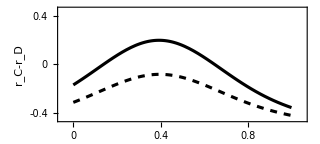

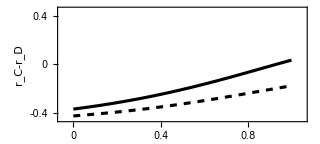

```mathematica
rC[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])]-κ;
rD[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)])];

γ=1.0;
κ=0.5;

p[σ_,β_]:=Plot[
{
rC[y,β,σ,15]-rD[y,β,σ,15],
rC[y,β,σ,25]-rD[y,β,σ,25]
},{y,0,1}
,PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Black,Dashed}}
,Frame->True
,PlotRange->{{-0.05,1.05},{-0.45,0.45}}
,ImageSize->320
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.45
,FrameLabel->{{"r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}
]

Show[p[2,5]]
Show[p[3,2]]
```

```mathematica
γ=1.0;
κ=0.1;

rC[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (1+y(n-1))/n-σ)])]-κ;
rD[y_,β_,σ_,n_]:=γ If[n==0,1+ⅇ^σ,(1+ⅇ^σ)/(1+Exp[-(β (y(n-1))/n-σ)])];
y0=0.1;
Manipulate[
Plot[
{
rC[y,β,σ,n]-rD[y,β,σ,n]
},{y,0,1}
,PlotStyle->{{Thickness[0.007],Black},{Thickness[0.007],Red,Dashed}}
,Frame->True
,PlotRange->All
,ImageSize->320
,LabelStyle->{FontSize->16,Black,FontFamily->"Arial"}
,FrameStyle->Directive[Thickness[0.004],Black]
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.85
(*,FrameLabel->{{"r_C-r_D",None},{"Frequency of C",None(*"n=8, σ=β/2"*)}}*)
,Axes->{True,False}
,AxesStyle->{Thickness[0.0035],Opacity[0.5,Gray]}
(*,PlotLegends->{Placed[{"n=15","n=25"},{0.8,0.75}]}*)
]
,{{σ,2},-10,100,0.1}
,{{β,2},0,10,0.01}
,{{n,5},0,100,1}
]
```